# KoenderColor: Interactive Exploration

Exploration and experimentation with the 3D empirical color metric field from Koenderink et al. (2026).

## 1. Setup & Package Loading

```mathematica
PacletDirectoryLoad[ParentDirectory[NotebookDirectory[]]];
Needs["KoenderColor`"]
```

## 2. Inspecting Empirical Data (35 BCC Lattice Points)

```mathematica
Short[KoenderinkData["sRGB"],5]
```

{<|Point→{0.2,0.2,0.2},Sigma→{{5921/10000000,487/2500000,29/312500},{487/2500000,1943/5000000,1021/10000000},{29/312500,1021/10000000,4749/10000000}},RawInteger→<|mu→{200,200,200},SigmaUpper→{5921,1948,928,3886,1021,4749}|>|>,«33»,<|Point→{0.8,0.8,0.8},Sigma→{«1»},RawInteger→<|mu→{800,800,800},SigmaUpper→{«1»}|>|>}

## 3. 3D Visualization of Empirical Metric Field (Paper Figure 8)

```mathematica
Graphics3D[{Map[{Apply[RGBColor,#],Opacity[0.7],Specularity[White,20],KoenderinkEllipsoid[#,"Scale"->2.0]}&,KoenderinkData["Points"]]},BoxRatios->{1,1,1},Axes->True,AxesLabel->{"R","G","B"},PlotRange->{{0,1},{0,1},{0,1}},Background->GrayLevel[0.15]]
```

-Graphics3D-

## 4. Evaluating Metric Tensor and Color Distance

```mathematica
c1=RGBColor[0.5,0.5,0.5];
c2=RGBColor[0.55,0.5,0.5];
Print["Midpoint Riemannian chord distance: ",KoenderinkColorDistance[c1,c2]];
Print["Line-integral arc length: ",KoenderinkColorDistance[c1,c2,"Method"->"LineIntegral"]];
```

Midpoint Riemannian chord distance: 1.4942

Line-integral arc length: 1.49225

## 5. Distance along the Achromatic Diagonal (Paper Figure 13)

```mathematica
grayPts=Table[{g,g,g},{g,0.2,0.8,0.05}];
vols=Map[Det[KoenderinkMetricMatrix[#]]^(1/2)&,grayPts];
```

```mathematica
vols
```

{0.0000167994,0.0000248634,0.0000333038,0.0000387316,0.0000424323,0.0000447665,0.0000469022,0.0000509139,0.0000548583,0.0000570749,0.0000597045,0.000062433,0.0000630353}

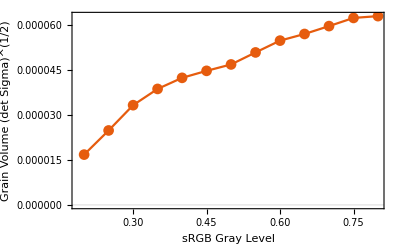

```mathematica
ListLinePlot[Transpose[{grayPts[[All,1]],vols}],PlotMarkers->Automatic,AxesLabel->{"sRGB Gray Level","Grain Volume (det Sigma)^(1/2)"},PlotTheme->"Scientific"]
```